```mathematica
AugmentedFormula[form_,edge_,full_]:=ImpliedNodes[Map[SymbolReplace[#,edge]&,form],full]
```

```mathematica
DrawAugmented[form_]:=Block[{labels=Map[#[[1]]->Rotate[Labeled[SymbolToLabel[#[[1]]],Style[#[[2]],Red]],Pi/6]&,Tally[form]]},
Graph[FormulaGraphReverse2[form],VertexLabels->labels,ImageSize->650]
]
```

```mathematica
Sinks[g_]:=Select[VertexList[g],SymbolLevel[#]==4&]
```

```mathematica
AlmostSinks[g_]:=With[{s=Sinks[g]//First},Select[VertexList[VertexInComponent[g,s]],#=!=s&]]
```

```mathematica
AlmostSinks[g_]:=With[{s=Sinks[g]},DeleteDuplicates[Flatten[Table[Select[VertexInComponent[g,v,1],#=!=v&],{v,s}]]]]
```

```mathematica
With[{g=MinimalGraph[5]},
With[{full=FindFullFormula[g]},
{full,
Table[AugmentedFormula[FindFullFormula[EdgeContract[g,e]],e,full],{e,EdgeList[g]}]//Flatten//Tally
}
]
]
```

{{v1x2x3x4x5x6,v1x2x3x46x5,v1x2x36x4x5,v1x2x35x4x6,v1x2x35x46},{{v1x2x3x4x5x6,12},{v1x2x3x46x5,6},{v1x2x36x4x5,8},{v1x2x35x4x6,6},{v1x2x35x46,1}}}

```mathematica
AlmostSinks[FormulaGraphReverse2[FindFullFormula[MinimalGraph[6]]]]
```

{v1x2x357x46,v1x2x357x4x6,v1x2x35x46x7,v1x2x37x46x5,v1x2x3x46x57}

```mathematica
VertexInComponent[FormulaGraphReverse2[FindFullFormula[CycleGraph[6]]],v1x2x3x4x5x6,2]
```

{v1x2x3x4x5x6}

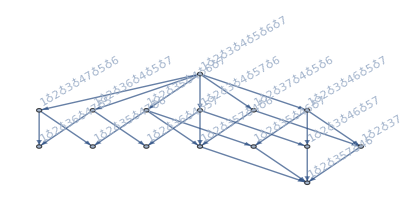
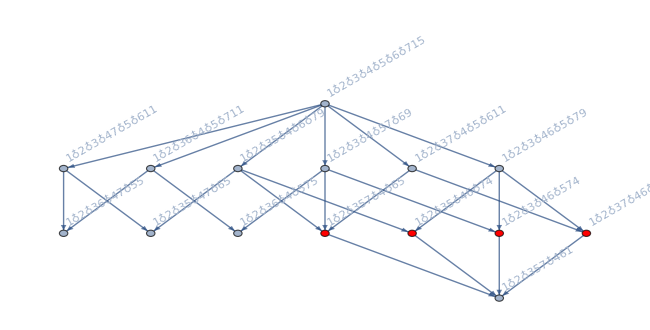
{-Graphics-,{v1x2x357x4x6,v1x2x35x46x7,v1x2x37x46x5,v1x2x3x46x57},{v1x2x357x46},-Graphics-}

```mathematica
With[{g=MinimalGraph[6]},
With[{full=FindFullFormula[g]},
{FormulaGraphReverse2[full],
AlmostSinks[FormulaGraphReverse2[full]],
Sinks[FormulaGraphReverse[full]],
Graph[DrawAugmented[Flatten[Table[AugmentedFormula[FindFullFormula[EdgeContract[g,e]],e,full],{e,EdgeList[g]}]]],VertexStyle->Table[v->Red,{v,AlmostSinks[FormulaGraphReverse2[full]]}]]
}
]
]
```

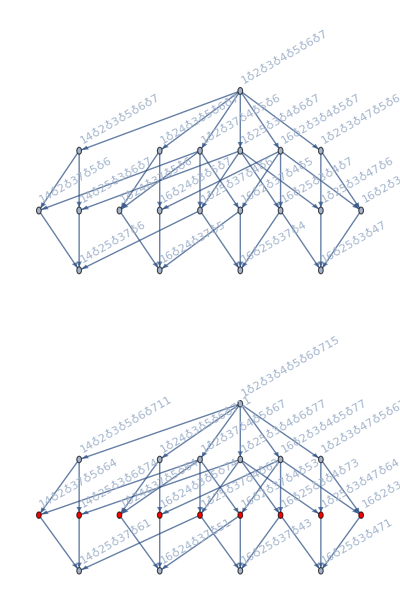

```mathematica
With[{g=ReadGrof[6]},
With[{full=FindFullFormula[g]},
{Graph[FormulaGraphReverse2[full],ImageSize->600],
Graph[DrawAugmented[Flatten[Table[AugmentedFormula[FindFullFormula[EdgeContract[g,e]],e,full],{e,EdgeList[g]}]]],VertexStyle->Table[v->Red,{v,AlmostSinks[FormulaGraphReverse2[full]]}]]
}
]
]//Column
```

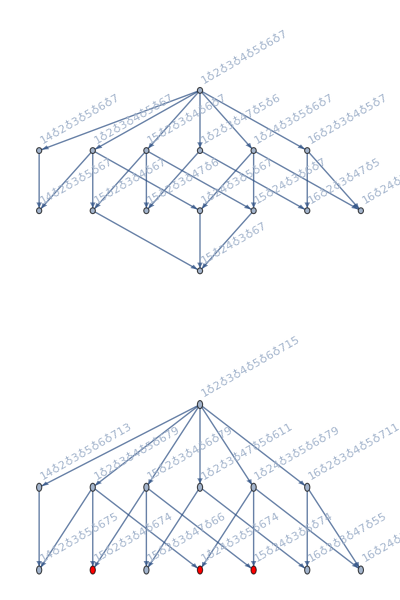

```mathematica
With[{g=ReadGrof[5]},
With[{full=FindFullFormula[g]},
{Graph[FormulaGraphReverse2[full],ImageSize->600],
Graph[DrawAugmented[Flatten[Table[AugmentedFormula[FindFullFormula[EdgeContract[g,e]],e,full],{e,EdgeList[g]}]]],VertexStyle->Table[v->Red,{v,AlmostSinks[FormulaGraphReverse2[full]]}]]
}
]
]//Column
```

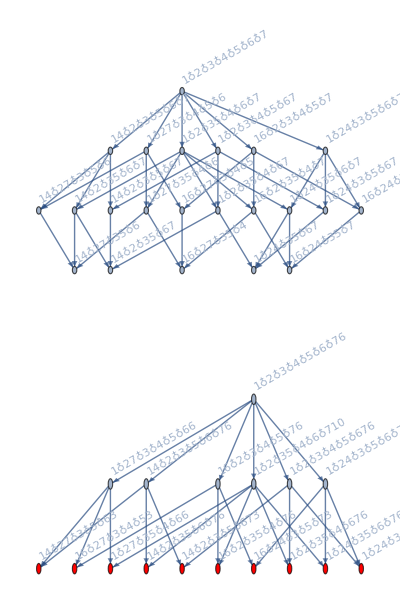

```mathematica
With[{g=ReadGrof[7]},
With[{full=FindFullFormula[g]},
{Graph[FormulaGraphReverse2[full],ImageSize->600],
Graph[DrawAugmented[Flatten[Table[AugmentedFormula[FindFullFormula[VertexContract[g,{e[[1]],e[[2]]}]],e,full],{e,EdgeList[GraphComplement[g]]}]]],VertexStyle->Table[v->Red,{v,AlmostSinks[FormulaGraphReverse2[full]]}]]
}
]
]//Column
```

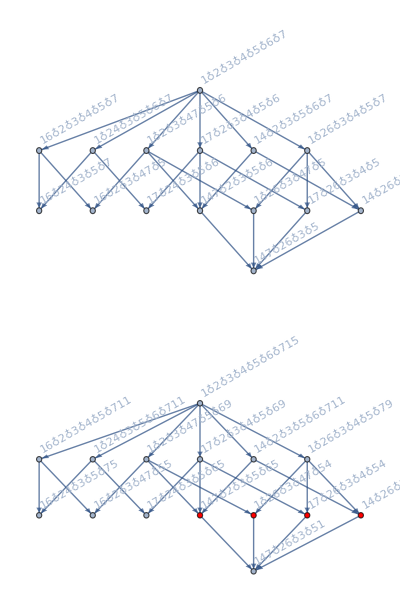

```mathematica
With[{g=ReadGrof[8]},
With[{full=FindFullFormula[g]},
{Graph[FormulaGraphReverse2[full],ImageSize->600],
Graph[DrawAugmented[Flatten[Table[AugmentedFormula[FindFullFormula[EdgeContract[g,e]],e,full],{e,EdgeList[g]}]]],VertexStyle->Table[v->Red,{v,AlmostSinks[FormulaGraphReverse2[full]]}]]
}
]
]//Column
```

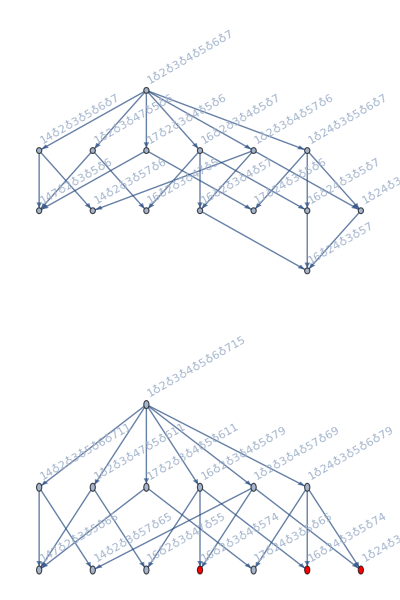

```mathematica
With[{g=ReadGrof[9]},
With[{full=FindFullFormula[g]},
{Graph[FormulaGraphReverse2[full],ImageSize->600],
Graph[DrawAugmented[Flatten[Table[AugmentedFormula[FindFullFormula[EdgeContract[g,e]],e,full],{e,EdgeList[g]}]]],VertexStyle->Table[v->Red,{v,AlmostSinks[FormulaGraphReverse2[full]]}]]
}
]
]//Column
```

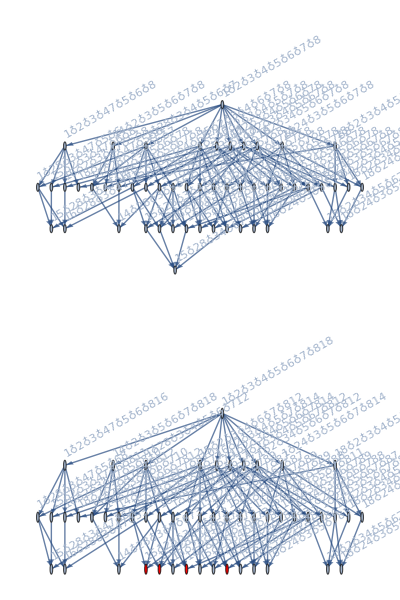

```mathematica
With[{g=ReadGrof[10]},
With[{full=FindFullFormula[g]},
{Graph[FormulaGraphReverse2[full],ImageSize->600],
Graph[DrawAugmented[Flatten[Table[AugmentedFormula[FindFullFormula[EdgeContract[g,e]],e,full],{e,EdgeList[g]}]]],VertexStyle->Table[v->Red,{v,AlmostSinks[FormulaGraphReverse2[full]]}]]
}
]
]//Column
```

```mathematica
GatherBy[{{1,2},{2,3},{4,2}},Last[#1]==Last[#1]&]
```

{{{1,2},{2,3},{4,2}}}

```mathematica
Map[Map[First,#]&,Gather[With[{g=ReadGrof[10]},
With[{full=FindFullFormula[g]},
Join[
Table[e->Sort[Map[SymbolToSets,AugmentedFormula[FindFullFormula[VertexContract[g,{e[[1]],e[[2]]}]],e,full]]],{e,EdgeList[GraphComplement[g]]}],
Table[e->Sort[AugmentedFormula[FindFullFormula[EdgeContract[g,e]],e,full],CompareSymbolsNew],{e,EdgeList[g]}]
]
]
],Last[#1]==Last[#2]&]]
```

{{1<->5},{1<->6},{1<->8},{1<->4},{2<->8},{2<->4},{3<->4},{7<->6},{7<->8},{7<->4},{1<->2},{1<->3},{1<->7},{2<->3},{2<->5},{2<->6},{2<->7},{3<->5},{3<->6},{3<->7},{3<->8},{4<->5},{4<->6},{4<->8},{5<->6},{5<->7},{5<->8},{6<->8}}

```mathematica
Map[Map[First,#]&,
Gather[With[{g=ReadGrof[10]},
With[{full=FindFullFormula[g]},
Join[
Table[Style[e,Blue]->Sort[Map[SymbolToSets,AugmentedFormula[FindFullFormula[VertexContract[g,{e[[1]],e[[2]]}]],e,full]]],{e,EdgeList[GraphComplement[g]]}],
Table[e->Sort[Map[SymbolToSets,AugmentedFormula[FindFullFormula[EdgeContract[g,e]],e,full]]],{e,EdgeList[g]}]
]
]
],Last[#1]==Last[#2]&]
]
```

{{1<->5},{1<->6},{1<->8},{1<->4},{2<->8},{2<->4},{3<->4},{7<->6},{7<->8},{7<->4},{1<->2},{1<->3},{1<->7},{2<->3},{2<->5},{2<->6},{2<->7},{3<->5},{3<->6},{3<->7},{3<->8},{4<->5},{4<->6},{4<->8},{5<->6},{5<->7},{5<->8},{6<->8}}

```mathematica
Map[Map[First,#]&,
Gather[With[{g=MinimalGraph[5]},
With[{full=FindFullFormula[g]},
Join[
Table[Style[e,Blue]->Sort[Map[SymbolToSets,AugmentedFormula[FindFullFormula[VertexContract[g,{e[[1]],e[[2]]}]],e,full]]],{e,EdgeList[GraphComplement[g]]}],
Table[e->Sort[Map[SymbolToSets,AugmentedFormula[FindFullFormula[EdgeContract[g,e]],e,full]]],{e,EdgeList[g]}]
]
]
],Last[#1]==Last[#2]&]
]
```

{{3<->5,4<->6},{3<->6},{1<->2},{1<->3,3<->2},{1<->4,2<->4,5<->6},{3<->4,1<->5,2<->5},{4<->5},{1<->6,2<->6}}

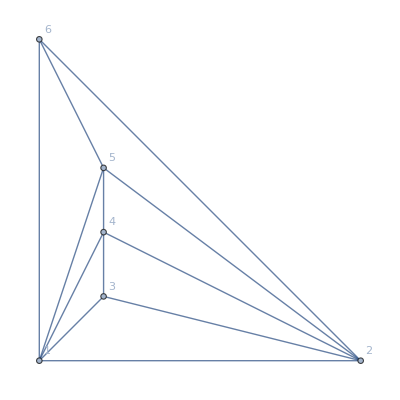

```mathematica
MinimalGraph[5]
```

```mathematica
Map[Map[First,#]&,
Gather[With[{g=JacobsThalGraph[5]},
With[{full=FindFullFormula[g]},
Join[
Table[Style[e,Blue]->Sort[Map[SymbolToSets,AugmentedFormula[FindFullFormula[VertexContract[g,{e[[1]],e[[2]]}]],e,full]]],{e,EdgeList[GraphComplement[g]]}],
Table[e->Sort[Map[SymbolToSets,AugmentedFormula[FindFullFormula[EdgeContract[g,e]],e,full]]],{e,EdgeList[g]}]
]
]
],Last[#1]==Last[#2]&]
]
```

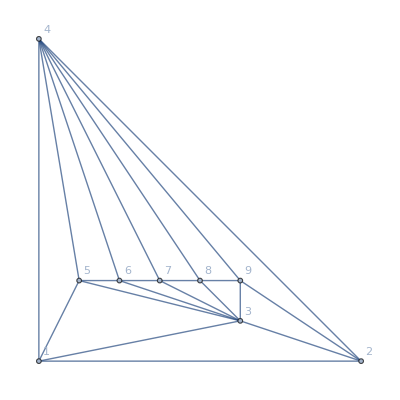

```mathematica
Graph[JacobsThalGraph[5],GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]
```

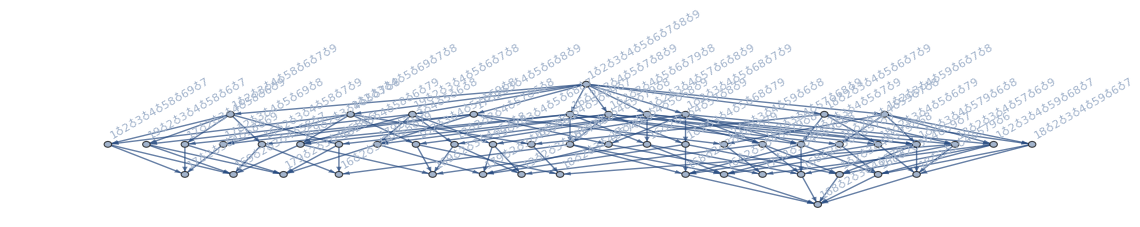

```mathematica
With[{g=JacobsThalGraph[5],e=2<->4},
With[{full=FindFullFormula[g]},
AugmentedFormula[FindFullFormula[EdgeContract[g,e]],e,full]
]
]//FormulaGraphReverse2
```

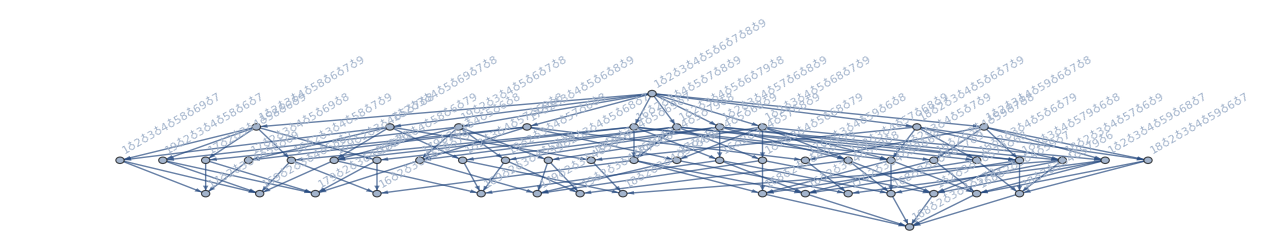

```mathematica
With[{g=JacobsThalGraph[5],e=3<->2},
With[{full=FindFullFormula[g]},
AugmentedFormula[FindFullFormula[EdgeContract[g,e]],e,full]
]
]//FormulaGraphReverse2
```

```mathematica
Map[Map[First,#]&,
Gather[With[{g=ReadGrof[4]},
With[{full=FindFullFormula[g]},
Join[
Table[Style[e,Blue]->Sort[Map[SymbolToSets,AugmentedFormula[FindFullFormula[VertexContract[g,{e[[1]],e[[2]]}]],e,full]]],{e,EdgeList[GraphComplement[g]]}],
Table[e->Sort[Map[SymbolToSets,AugmentedFormula[FindFullFormula[EdgeContract[g,e]],e,full]]],{e,EdgeList[g]}]
]
]
],Last[#1]==Last[#2]&]
]
```

{{1<->4},{2<->5},{3<->6},{1<->2,1<->5,2<->4,4<->5},{1<->3,1<->6,3<->4,4<->6},{2<->3,2<->6,3<->5,5<->6}}

```mathematica
Map[Map[First,#]&,
Gather[With[{g=ReadGrof[3]},
With[{full=FindFullFormula[g]},
Join[
Table[Style[e,Blue]->Sort[Map[SymbolToSets,AugmentedFormula[FindFullFormula[VertexContract[g,{e[[1]],e[[2]]}]],e,full]]],{e,EdgeList[GraphComplement[g]]}],
Table[e->Sort[Map[SymbolToSets,AugmentedFormula[FindFullFormula[EdgeContract[g,e]],e,full]]],{e,EdgeList[g]}]
]
]
],Last[#1]==Last[#2]&]
]
```

{{1<->6,2<->4},{1<->4},{1<->2,3<->6,5<->6},{1<->3,1<->5},{2<->3,2<->5,4<->6},{2<->6},{3<->4,4<->5},{3<->5}}

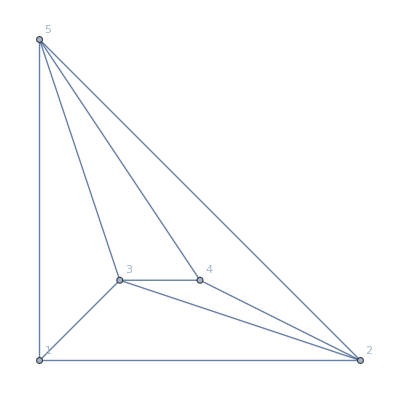
-Graphics-→{{1<->4,1<->2,1<->3,1<->5,2<->4,3<->4,4<->5},{2<->3,2<->5,3<->5}}

```mathematica
With[{g=ReadGrof[2]},
With[{full=FindFullFormula[g]},
Graph[g,GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]->Map[Map[First,#]&,
Gather[Join[
Table[Style[e,Blue]->Sort[Map[SymbolToSets,AugmentedFormula[FindFullFormula[VertexContract[g,{e[[1]],e[[2]]}]],e,full]]],{e,EdgeList[GraphComplement[g]]}],
Table[e->Sort[Map[SymbolToSets,AugmentedFormula[FindFullFormula[EdgeContract[g,e]],e,full]]],{e,EdgeList[g]}]
],Last[#1]==Last[#2]&]
]
]
]
```

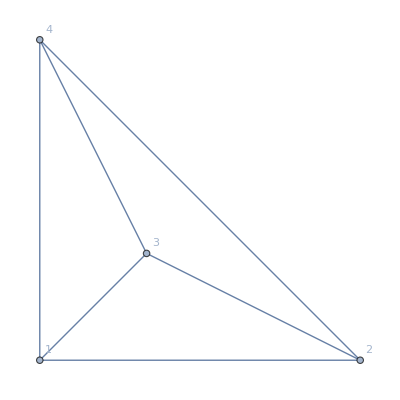
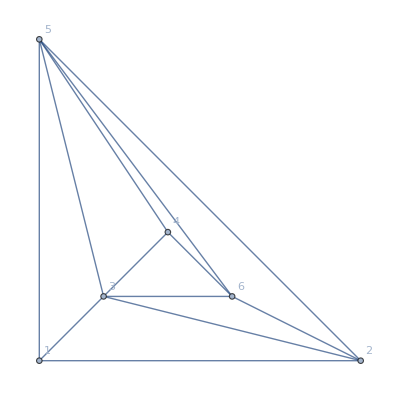
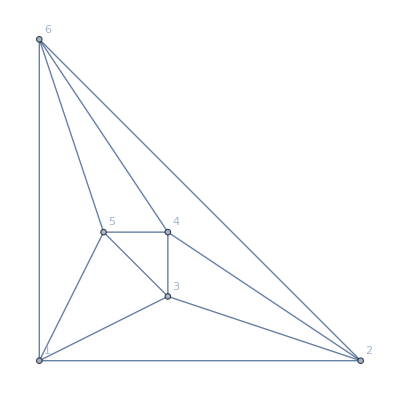
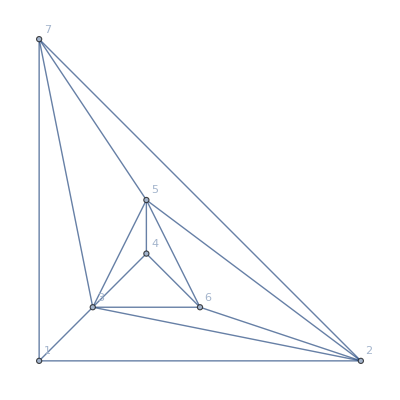
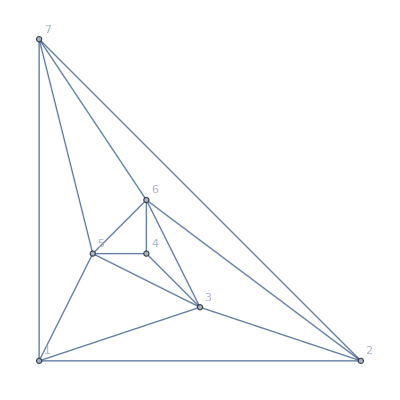
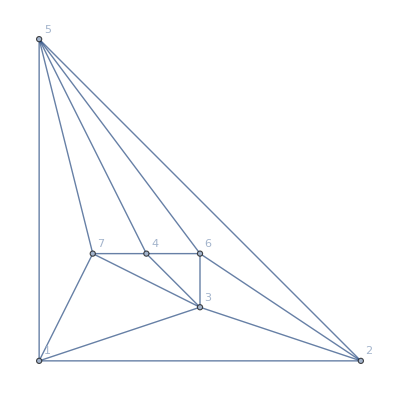
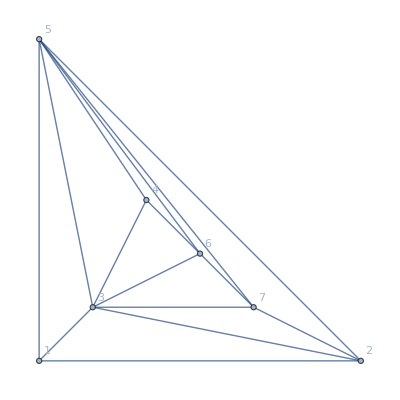
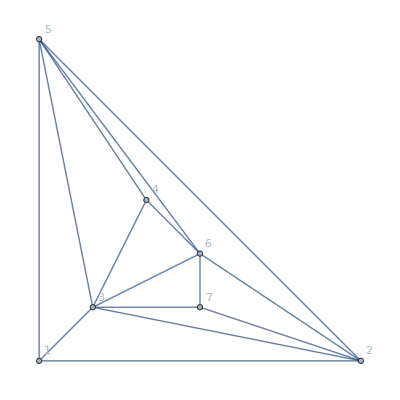
{-Graphics-→{{1<->2,1<->3,1<->4,2<->3,2<->4,3<->4}},-Graphics-→{{1<->4,1<->2,1<->3,1<->5,2<->4,3<->4,4<->5},{2<->3,2<->5,3<->5}},-Graphics-→{{1<->6,2<->4},{1<->4},{1<->2,3<->6,5<->6},{1<->3,1<->5},{2<->3,2<->5,4<->6},{2<->6},{3<->4,4<->5},{3<->5}},-Graphics-→{{1<->4},{2<->5},{3<->6},{1<->2,1<->5,2<->4,4<->5},{1<->3,1<->6,3<->4,4<->6},{2<->3,2<->6,3<->5,5<->6}},-Graphics-→{{1<->5},{1<->6},{1<->4},{2<->4},{7<->6},{7<->4},{1<->2},{1<->3},{1<->7},{2<->3},{2<->5},{2<->6},{2<->7,5<->6},{3<->4},{3<->5},{3<->6},{3<->7},{4<->5},{4<->6},{5<->7}},-Graphics-→{{1<->6},{1<->4},{2<->5},{2<->4},{3<->7},{7<->4},{1<->2,5<->6},{1<->3},{1<->5},{1<->7,3<->6},{2<->3},{2<->6},{2<->7,3<->5},{3<->4},{4<->5},{4<->6},{5<->7},{6<->7}},-Graphics-→{{1<->6},{1<->4},{2<->7},{2<->4},{3<->5},{7<->6},{1<->2},{1<->3,1<->5},{1<->7},{2<->3,2<->5},{2<->6},{3<->4,4<->5},{3<->6,5<->6},{3<->7,5<->7},{4<->6},{4<->7}},-Graphics-→{{1<->7},{1<->4},{1<->6},{2<->4},{2<->6},{7<->4},{1<->2},{1<->3,1<->5},{2<->3,2<->5},{2<->7},{3<->4,4<->5},{3<->5},{3<->6,5<->6},{3<->7,5<->7},{4<->6},{6<->7}},-Graphics-→{{1<->6},{1<->7},{1<->4},{2<->4},{5<->7},{7<->4},{1<->2},{1<->3},{1<->5},{2<->3},{2<->5},{2<->6},{2<->7},{3<->4},{3<->5},{3<->6},{3<->7},{4<->5},{4<->6},{5<->6},{6<->7}},-Graphics-→{{1<->5},{1<->6},{1<->8},{1<->4},{2<->8},{2<->4},{3<->4},{7<->6},{7<->8},{7<->4},{1<->2},{1<->3},{1<->7},{2<->3},{2<->5},{2<->6},{2<->7},{3<->5},{3<->6},{3<->7},{3<->8},{4<->5},{4<->6},{4<->8},{5<->6},{5<->7},{5<->8},{6<->8}},-Graphics-→{{1<->5},{1<->6},{1<->4},{1<->8},{2<->4},{2<->8},{3<->5},{7<->6},{7<->4},{6<->8},{1<->2},{1<->3},{1<->7},{2<->3},{2<->5},{2<->6},{2<->7},{3<->4},{3<->6},{3<->7},{3<->8},{4<->5},{4<->6},{4<->8},{5<->6},{5<->7},{5<->8},{7<->8}},-Graphics-→{{1<->5},{1<->6},{1<->4},{1<->8},{2<->4},{2<->8},{7<->6},{7<->4},{7<->8},{5<->4},{1<->2},{1<->3},{1<->7},{2<->3},{2<->5},{2<->6},{2<->7},{3<->4},{3<->5},{3<->6},{3<->7},{3<->8},{4<->6},{4<->8},{5<->6},{5<->7},{5<->8},{6<->8}},-Graphics-→{{1<->5},{1<->8},{1<->4},{1<->6},{2<->4},{2<->6},{7<->8},{7<->4},{7<->6},{8<->4},{1<->2},{1<->3},{1<->7},{2<->3},{2<->5},{2<->7},{2<->8},{3<->4},{3<->5},{3<->6},{3<->7},{3<->8},{4<->5},{4<->6},{5<->6},{5<->7},{5<->8},{6<->8}},-Graphics-→{{1<->5},{1<->6},{1<->8},{1<->4},{2<->4},{3<->6},{7<->6},{7<->8},{7<->4},{5<->8},{1<->2},{1<->3},{1<->7},{2<->3},{2<->5},{2<->6},{2<->7},{2<->8},{3<->4},{3<->5},{3<->7},{3<->8},{4<->5},{4<->6},{4<->8},{5<->6},{5<->7},{6<->8}},-Graphics-→{{1<->6},{1<->8},{1<->4},{1<->5},{2<->4},{2<->5},{3<->8},{7<->6},{7<->4},{8<->4},{1<->2},{1<->3},{1<->7},{2<->3},{2<->6},{2<->7,5<->6},{2<->8},{3<->4},{3<->5},{3<->6},{3<->7},{4<->5},{4<->6},{5<->7},{5<->8},{6<->8},{7<->8}}}

```mathematica
Table[With[{g=ReadGrof[k]},
With[{full=FindFullFormula[g]},
Graph[g,GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]->Map[Map[First,#]&,
Gather[Join[
Table[Style[e,Blue]->Sort[Map[SymbolToSets,AugmentedFormula[FindFullFormula[VertexContract[g,{e[[1]],e[[2]]}]],e,full]]],{e,EdgeList[GraphComplement[g]]}],
Table[e->Sort[Map[SymbolToSets,AugmentedFormula[FindFullFormula[EdgeContract[g,e]],e,full]]],{e,EdgeList[g]}]
],Last[#1]==Last[#2]&]
]
]
],{k,15}]
```

```mathematica
Map[Map[First,#]&,
Gather[With[{g=ReadGrof[2]},
With[{full=FindFullFormula[g]},
Join[
Table[Style[e,Blue]->Sort[Map[SymbolToSets,AugmentedFormula[FindFullFormula[VertexContract[g,{e[[1]],e[[2]]}]],e,full]]],{e,EdgeList[GraphComplement[g]]}],
Table[e->Sort[Map[SymbolToSets,AugmentedFormula[FindFullFormula[EdgeContract[g,e]],e,full]]],{e,EdgeList[g]}]
]
]
],Last[#1]==Last[#2]&]
]
```

{{1<->4,1<->2,1<->3,1<->5,2<->4,3<->4,4<->5},{2<->3,2<->5,3<->5}}

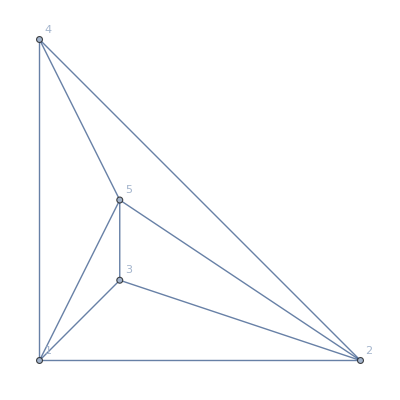
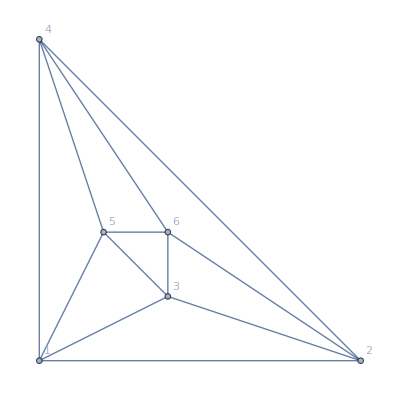
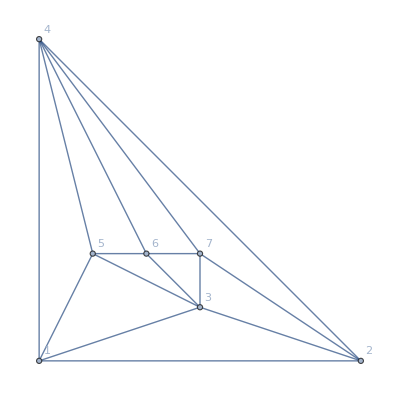
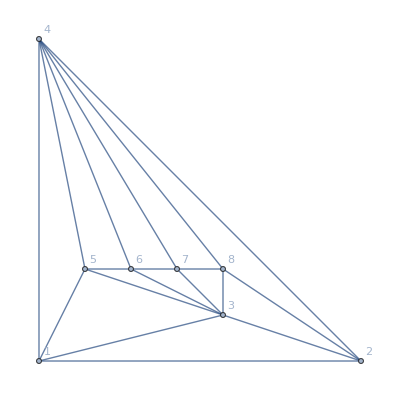
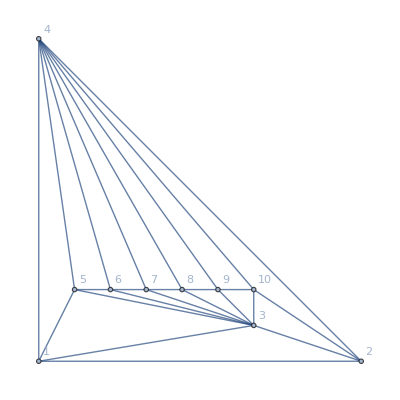
{-Graphics-→{{3<->4,3<->2,3<->1,1<->4,2<->4,5<->3,5<->4},{1<->2,5<->1,5<->2}},-Graphics-→{{1<->6},{2<->5},{3<->4},{1<->2,5<->1,6<->2,6<->5},{3<->2,2<->4,5<->4,5<->3},{3<->1,1<->4,6<->3,6<->4}},-Graphics-→{{1<->7},{1<->6},{2<->5},{2<->6},{3<->4},{5<->7},{1<->2},{3<->2,2<->4},{3<->1,1<->4},{5<->1},{7<->2},{7<->3,7<->4},{5<->4,5<->3},{6<->5},{6<->3,6<->4},{7<->6}},-Graphics-→{{1<->8},{1<->6},{1<->7},{2<->5},{2<->6},{2<->7},{3<->4},{5<->8},{5<->7},{8<->6},{1<->2},{3<->2,2<->4},{3<->1,1<->4},{5<->1},{8<->2},{8<->3,8<->4},{5<->4,5<->3},{6<->5},{6<->3,6<->4},{7<->6},{7<->3,7<->4},{8<->7}},-Graphics-→{{1<->9},{1<->6},{1<->7},{1<->8},{2<->5},{2<->6},{2<->7},{2<->8},{3<->4},{5<->9},{5<->7},{5<->8},{9<->6},{9<->7},{6<->8},{1<->2},{3<->2,2<->4},{3<->1,1<->4},{5<->1},{9<->2},{9<->3,9<->4},{5<->4,5<->3},{6<->5},{6<->3,6<->4},{7<->6},{7<->3,7<->4},{8<->7},{8<->3,8<->4},{9<->8}},-Graphics-→{{1<->10},{1<->6},{1<->7},{1<->8},{1<->9},{2<->5},{2<->6},{2<->7},{2<->8},{2<->9},{3<->4},{5<->10},{5<->7},{5<->8},{5<->9},{10<->6},{10<->7},{10<->8},{6<->8},{6<->9},{7<->9},{1<->2},{3<->2,2<->4},{3<->1,1<->4},{5<->1},{10<->2},{10<->3,10<->4},{5<->4,5<->3},{6<->5},{6<->3,6<->4},{7<->6},{7<->3,7<->4},{8<->7},{8<->3,8<->4},{9<->8},{9<->3,9<->4},{10<->9}}}

```mathematica
Monitor[Table[With[{g=JacobsThalGraph[k]},
With[{full=FindFullFormula[g]},
Graph[g,GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]->Map[Map[First,#]&,
Gather[Join[
Table[Style[e,Blue]->Sort[Map[SymbolToSets,AugmentedFormula[FindFullFormula[VertexContract[g,{e[[1]],e[[2]]}]],e,full]]],{e,EdgeList[GraphComplement[g]]}],
Table[e->Sort[Map[SymbolToSets,AugmentedFormula[FindFullFormula[EdgeContract[g,e]],e,full]]],{e,EdgeList[g]}]
],Last[#1]==Last[#2]&]
]
]
],{k,6}],{k,e}]
```

```mathematica
Differences[{2,6,16,22,29}]
```

{4,10,6,7}

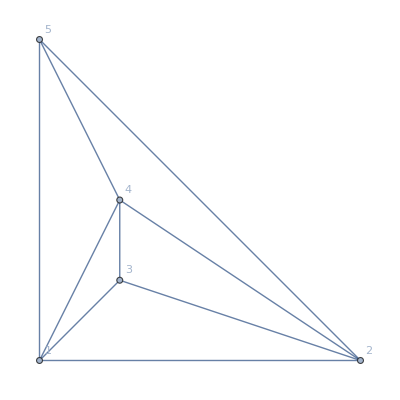
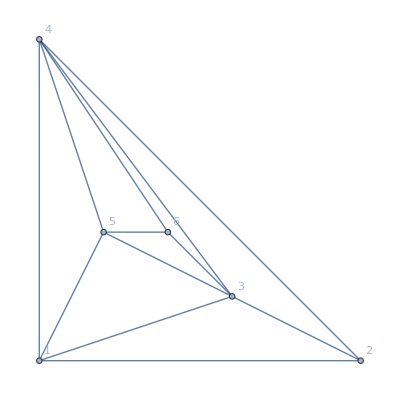
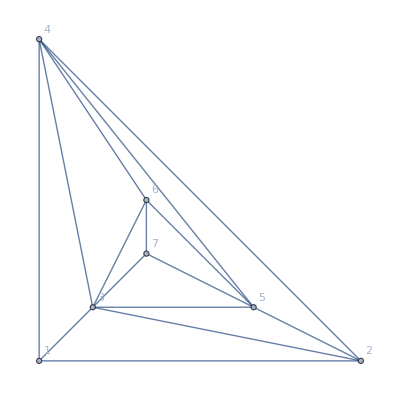
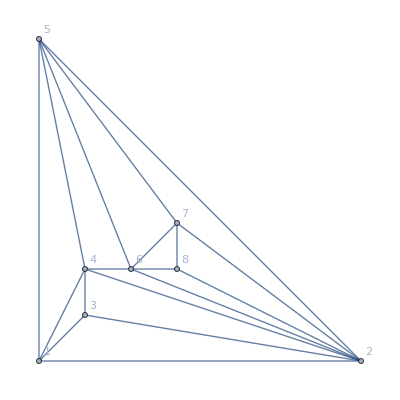
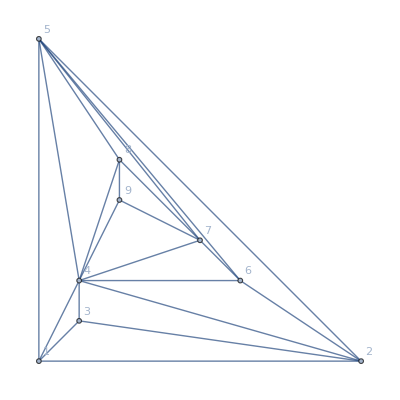
{-Graphics-→{{1<->2,1<->3,3<->2,1<->4,2<->4,3<->4}},-Graphics-→{{3<->5,1<->3,3<->2,3<->4,1<->5,2<->5,4<->5},{1<->2,1<->4,2<->4}},-Graphics-→{{1<->6,2<->5},{2<->6},{1<->2,3<->5,4<->5},{1<->3,1<->4,5<->6},{3<->2,2<->4},{3<->4},{1<->5},{3<->6,4<->6}},-Graphics-→{{1<->5},{1<->6},{1<->7},{2<->6},{2<->7},{4<->7},{1<->2},{1<->3},{3<->2},{1<->4},{2<->4,5<->6},{3<->4},{2<->5},{3<->5},{4<->5},{3<->6},{4<->6},{3<->7},{5<->7},{6<->7}},-Graphics-→{{1<->6},{1<->7},{1<->8},{3<->5},{3<->6},{3<->7},{3<->8},{4<->7},{4<->8},{5<->8},{1<->2},{1<->3},{3<->2},{1<->4},{2<->4},{3<->4},{1<->5},{2<->5},{4<->5},{2<->6},{4<->6},{5<->6},{2<->7},{5<->7},{6<->7},{2<->8},{6<->8},{7<->8}},-Graphics-→{{1<->6},{1<->7},{1<->8},{1<->9},{2<->7},{2<->8},{2<->9},{3<->5},{3<->6},{3<->7},{3<->8},{3<->9},{5<->9},{6<->8},{6<->9},{1<->2},{1<->3},{3<->2},{1<->4},{2<->4},{3<->4},{1<->5},{2<->5},{4<->5},{2<->6},{4<->6},{5<->6},{4<->7},{5<->7},{6<->7},{4<->8},{5<->8},{7<->8},{4<->9},{7<->9},{8<->9}}}

```mathematica
Monitor[Table[With[{g=MinimalGraph2[k]},
With[{full=FindFullFormula[g]},
Graph[g,GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]->Map[Map[First,#]&,
Gather[Join[
Table[Style[e,Blue]->Sort[Map[SymbolToSets,AugmentedFormula[FindFullFormula[VertexContract[g,{e[[1]],e[[2]]}]],e,full]]],{e,EdgeList[GraphComplement[g]]}],
Table[e->Sort[Map[SymbolToSets,AugmentedFormula[FindFullFormula[EdgeContract[g,e]],e,full]]],{e,EdgeList[g]}]
],Last[#1]==Last[#2]&]
]
]
],{k,3,8}],{k,e}]
```